#### Setting up

```mathematica
Needs["MaTeX`"];
Needs["QuantumInformation`"];
```

```mathematica
Graphics`PlotMarkers[]
```

{{●,8.96},{■,8.96},{◆,10.88},{▲,10.24},{▼,10.24},{○,10.24},{□,10.24},{◇,10.24},{△,11.136},{▽,11.136}}

```mathematica
(* Set options for the plot *)
hexToRGB[hex_]:=RGBColor@@(N[FromDigits[StringJoin[#],12]/255]&/@Partition[Characters[hex],2]);

brightcolours = {RGBColor[0.03529411764705882, 0.4392156862745098, 0.32941176470588235],RGBColor[0.396078431372549, 0.6, 1.],RGBColor[1., 0.8705882352941177, 0.],RGBColor[1., 0.6, 0.]};
textbookcolours = {RGBColor[0.028, 0.5376, 0.5936],Hue[0.07, 1, 0.75],RGBColor[0.531753, 0.331477, 0.920616],RGBColor[0.627887, 0.708654, 0.],RGBColor[0.237882, 0.510711, 0.979357],RGBColor[0.975692, 0.628459, 0.0656322],RGBColor[0.629898, 0.28, 0.684772],RGBColor[0.198854, 0.7, 0.446913],RGBColor[0.910038, 0.300188, 0.226913],RGBColor[0.440765, 0.385541, 1.]};
colscheme10 = {RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275],RGBColor[0.09803921568627451, 0.06666666666666667, 0.25098039215686274],RGBColor[0.5607843137254902, 0.5254901960784314, 0.5647058823529412]};

blend = 2/4;
elementarycols = {Darker@Red, Darker@Darker@Green,  Blend[  {Darker@Red, Yellow},blend ], Blend[ {Darker@Darker@Green, Blue}, blend ] };


black = {Black, Black, Black};

cols = elementarycols[[{1,2}]];

(* Make very bare plots without units *)
SetOptions[ Plot
, BaseStyle -> {FontFamily-> "Helvetica", FontSize-> 14}
,Axes -> {False, False} 
, Frame -> {True, True, True, True} 
, FrameStyle -> Directive[ Black, Thickness[0.003 ] ]
, PlotTheme-> None
, FrameTicksStyle-> Directive[ 15, Black ]
, FrameTicks -> None
, AspectRatio-> 1/3
, ImageSize-> {600,200}
, GridLinesStyle -> Directive[ Gray, Thickness[ 0.005] ]
, PlotLegends -> None
];
```

## STIRAP basics

#### Pump and Stokes pulses

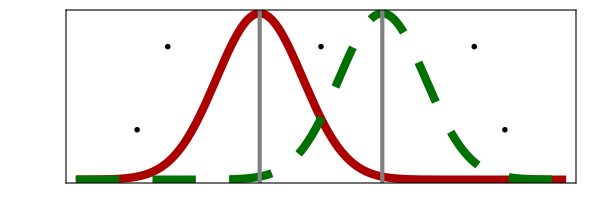

```mathematica
cols = elementarycols[[{1,2}]];
pltstyle = { Directive[ cols[[1]], Thickness[.01] ], Directive[cols[[2]], Thickness[.01], Dashing[{.052,.04}]] };
magn = 3.4;

fun1 = Exp[ - (t+1)^2 ];
fun2 = Exp[ - (t-1)^2 ];
stokespumpplt = Plot[ {fun1, fun2} , {t,-4,4}, GridLines->{{-1,1}, {}}
, PlotStyle->pltstyle
, PlotLabel->MaTeX["\\text{Coupling strengths}", Magnification->3]
, Epilog -> { 
Text[ MaTeX[ "\\Omega_P", Magnification->magn ], {3,.3} ]
, Text[ MaTeX[ "\\Omega_S", Magnification->magn ], {-3,.3} ] 
, Text[MaTeX["II", Magnification-> .8 magn], {0,.8}]
,Text[MaTeX["I", Magnification-> .8 magn], {-2.5,.8}]
,Text[MaTeX["III", Magnification->.8 magn], {2.5,.8}]
 }
]
```

```mathematica
Export[ "intro_stokesPumpPlot.pdf", stokespumpplt ]
```

intro_stokesPumpPlot.pdf

Simpler version in our protocols:

#### Eigenstates

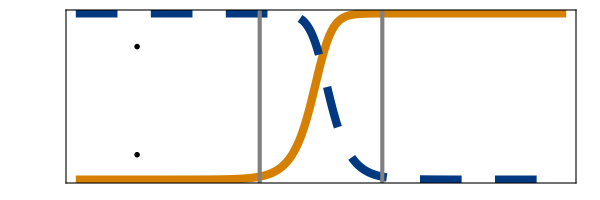

```mathematica
cols = elementarycols[[{3,4}]];
magn = 3.4;

pltstyle = { Directive[ cols[[1]], Thickness[.01] ], Directive[cols[[2]], Thickness[.01], Dashing[{.05,.04}]] };

v1 = 1/fun1;
v2 = 1/fun2;
v = Normalize[ {v1, v2} ];

estateplt = Plot[Evaluate@v, {t,-4,4}
,GridLines->{{-1,1}, {}}
, PlotStyle->pltstyle 
, PlotLabel->MaTeX["\\text{Dark state amplitude}", Magnification->3]
, Epilog -> { 
Text[ MaTeX[ "\\lvert 1 \\rangle", Magnification->magn ], {-3,.8} ]
,Text[ MaTeX[ "\\lvert 3 \\rangle", Magnification-> magn ], {-3,.15} ]

 }
]
```

```mathematica
Export[ "intro_estateplt.pdf", estateplt ]
```

intro_estateplt.pdf

#### Energy diagram

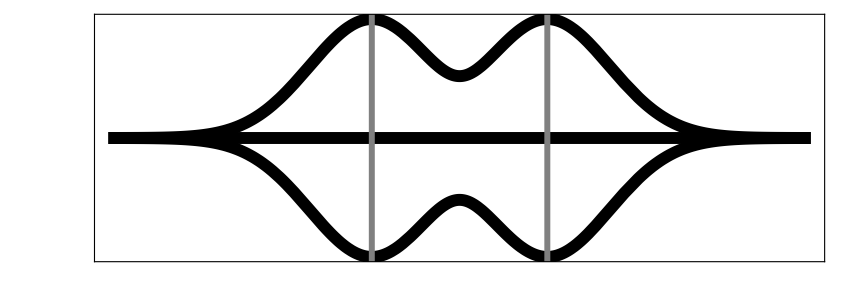

```mathematica
pltstyle = Directive[ Black, Thickness[0.01] ];


ham = {{ 0, fun1, 0}, {fun1, 0, fun2}, {0,fun2,0}};
evalplt = Plot[Evaluate@Eigenvalues[ham], {t,-4,4}
,GridLines->{{-1,1}, {}}
, PlotLabel->MaTeX["\\text{Energies}", Magnification->3]
, PlotStyle->pltstyle 
,  FrameTicks -> {{None,None}, {{{-4,MaTeX["0", Magnification->2]}, {4,MaTeX["T", Magnification->2]}}, None} }
, FrameLabel->{MaTeX["t", Magnification->2], None}
(* , Epilog -> { Text[ MaTeX[ "\\text{Energies } \\\\  \\lambda", Magnification->3.6  ], {-3,.87} ] } *)
]
```

```mathematica
Export[ "intro_evalplt.pdf", evalplt ]
```

intro_evalplt.pdf

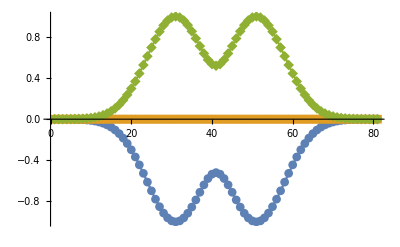

```mathematica
Ts = Range[-4,4,.1];
evals = Table[ Sort@Eigenvalues[ ham /. t-> tv ], {tv, Ts} ];
ListPlot[evalsᵀ]
```

## Tree graph plots

```mathematica
(* Assuming a flattened array with entries (p1, T, error), find for each p1 the optimal T *)
findTargetTimesFlat[ dataList_, targetEr_:.05 ]:= Module[{allparams, filtered, bestT},
	
	allparams = Sort@DeleteDuplicates[ dataList[[All,1]] ];
	Return[ Table[
		filtered = Select[ dataList, #[[1]] == allparams[[j]] && #[[3]] ≤ targetEr & ];
		bestT = Min[ filtered[[All,2]] ];
		{allparams[[j]], bestT}
	,{j,1,Length[allparams]}] ];
];
```

### Old stuff

```mathematica
resultfile =  FileNameJoin[ {NotebookDirectory[] ,"data", "CTAPtree_d2.dat"}]; 
resall = ReadList[ resultfile ] ;

nlevelss = DeleteDuplicates@resall[[All,1]];
Ts = DeleteDuplicates@resall[[All,2]];
```

ReadList::noopen: Cannot open /export/scratch1/groenlan/Dropbox/PhD/MATHEMATICA/CTAP/data/CTAPtree_d2.dat.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Evolution over time, for a specific nlevels

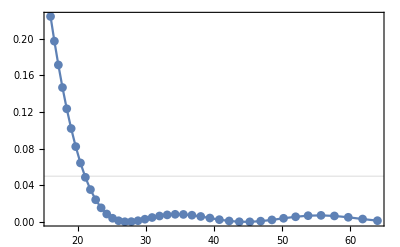

```mathematica
picknlevels = 4;
resfiltered = Select[ resall, #[[1]] == picknlevels & ];
resfiltered2 = SortBy[ resfiltered, #[[2]] & ];
ListPlot[ resfiltered2[[All,{2,3}]], GridLines->{{}, {.05}}
, Frame-> True
, PlotMarkers->Automatic ]
```

#### Pretty evolution over time

```mathematica
SetOptions[ ListPlot
, BaseStyle -> {FontFamily-> "Helvetica", FontSize-> 14}
, Frame -> {True, True, True, True} 
, FrameStyle -> Directive[ Black, Thickness[0.003 ] ]
, PlotTheme-> None
, FrameTicksStyle-> Directive[ 15, Black ]
, GridLinesStyle -> Directive[ Gray, Thickness[ 0.005] ]
,AspectRatio-> Automatic
, PlotLegends -> None
, Joined -> False
];
```

```mathematica
tartimes
```

{{1,10.9283},{2,15.455},{3,18.3792},{4,21.1121},{5,23.4254},{6,25.9921},{7,27.8576},{8,34.2968},{9,90.5097},{10,168.897},{11,274.374},{12,415.873}}

```mathematica
picknlevels = 4;
targettime = 21.1;
resfiltered = Select[ resall, #[[1]] == picknlevels && 17 < #[[2]] < 40& ];
resfiltered2 = SortBy[ resfiltered, #[[2]] & ];
errovsTimek4 = ListPlot[ resfiltered2[[All,{2,3}]], GridLines->{{}, {.05}}
, Frame-> True
, PlotMarkers->Automatic
, GridLinesStyle->Directive[ Opacity[.4],Thickness[0.01] ] 
, FrameLabel->{MaTeX["T/J", Magnification->2], MaTeX["\\mathcal{E}", Magnification->2]}
,FrameTicks -> {{ Automatic,Automatic },{Automatic, Automatic}} 
, Epilog-> Inset[ MaTeX[ "T^* = 21.1", Magnification->2 ], {30,.1}]
, ImageSize-> {300, 200}
]
```

Select::normal: Nonatomic expression expected at position 1 in Select[resall,#1⟦1⟧==picknlevels&&17<#1⟦2⟧<40&].

Part::partd: Part specification resall⟦2⟧ is longer than depth of object.

Part::partw: Part 2 of #1⟦1⟧==picknlevels&&17<#1⟦2⟧<40& does not exist.

Select::normal: Nonatomic expression expected at position 1 in Select[resall,#1⟦1⟧==picknlevels&&17<#1⟦2⟧<40&].

Part::partd: Part specification Select[resall,#1⟦1⟧==picknlevels&&17<#1⟦2⟧<40&]⟦All,{2,3}⟧ is longer than depth of object.

Select::normal: Nonatomic expression expected at position 1 in Select[resall,#1⟦1⟧==picknlevels&&17.<#1⟦2⟧<40.&].

Part::partd: Part specification Select[resall,#1⟦1⟧==picknlevels&&17.<#1⟦2⟧<40.&]⟦All,{2,3}⟧ is longer than depth of object.

Select::normal: Nonatomic expression expected at position 1 in Select[resall,#1⟦1⟧==picknlevels&&17.<#1⟦2⟧<40.&].

Part::partd: Part specification Select[resall,#1⟦1⟧==picknlevels&&17.<#1⟦2⟧<40.&]⟦All,{2,3}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPlot::lpn: Select[resall,#1⟦1⟧==picknlevels&&17.<#1⟦2⟧<40.&]⟦All,{2,3}⟧ is not a list of numbers or pairs of numbers.

Select::normal: Nonatomic expression expected at position 1 in Select[resall,#1⟦1⟧==picknlevels&&17.<#1⟦2⟧<40.&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

ListPlot::lpn: Select[resall,#1⟦1⟧==picknlevels&&17.<#1⟦2⟧<40.&]⟦All,{2,3}⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[Select[resall,#1⟦1⟧==picknlevels&&17<#1⟦2⟧<40&]⟦All,{2,3}⟧,GridLines→{{},{0.05}},Frame→True,PlotMarkers→Automatic,GridLinesStyle→Directive[Opacity[0.4],Thickness[0.01]],FrameLabel→{-Graphics-,-Graphics-},FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},Epilog→Inset[-Graphics-,{30,0.1}],ImageSize→{300,200}]

```mathematica
Export["errovsTimek4.pdf", errovsTimek4 ]
```

errovsTimek4.pdf

```mathematica
Export["khalf.pdf",MaTeX["k^{0.5}"]]
Export["ksixhalf.pdf",MaTeX["k^{6.5}"]]
```

khalf.pdf

ksixhalf.pdf

#### All in one contourplot

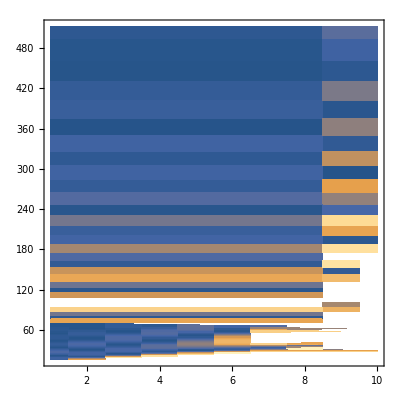

```mathematica
ListContourPlot[ resall, InterpolationOrder->0, Contours -> 1000 ]
```

#### Target times

```mathematica
SetOptions[ ListLogLogPlot
, BaseStyle -> {FontFamily-> "Helvetica", FontSize-> 14}
, Frame -> {True, True, True, True} 
, FrameStyle -> Directive[ Black, Thickness[0.003 ] ]
, PlotTheme-> None
, FrameTicksStyle-> Directive[ 15, Black ]
, AspectRatio->2/3
, ImageSize-> {400, 280}
, GridLinesStyle -> Directive[ Gray, Thickness[ 0.005] ]
, PlotLegends -> None
, Joined -> False
];
```

```mathematica
tartimes = findTargetTimesFlat[resall, .05 ];
fitlow = exponentFit[ tartimes[[2;;7]] ] 
fithigh = exponentFit[ tartimes[[8;;-2]] ] 
smalltstarplt =  Show[{
ListLogLogPlot[ tartimes[[1;;7]]
, PlotStyle->elementarycols[[4]]
, FrameLabel->{MaTeX["k", Magnification->2], MaTeX["T^*/J", Magnification->2]}
, FrameTicks -> {{Automatic, Automatic}, {Join[Range[1,4],{6,9,12}] ,  Automatic}}
, PlotRange->{{Min[tartimes[[All,1]] ], Max[tartimes[[All,1]] ]}, {Min[tartimes[[All,2]] ], Max[tartimes[[All,2]] ]}}
 ]
, LogLogPlot[ fitlow[[1]] * x ^ fitlow[[2]] , {x,1,Max[nlevelss]} , PlotStyle->{elementarycols[[1]], Dashed}]
}]
tstarplt = Show[{
ListLogLogPlot[ tartimes
, PlotStyle->elementarycols[[4]]
, FrameLabel->{MaTeX["k", Magnification->2], MaTeX["T^*/J", Magnification->2]}
, FrameTicks -> {{Automatic, Automatic}, {Join[Range[1,4],{6,9,12}] ,  Automatic}}
 ]
, LogLogPlot[ fitlow[[1]] * x ^ fitlow[[2]] , {x,1,Max[nlevelss]} , PlotStyle->{elementarycols[[1]], Dashed}]
, LogLogPlot[ fithigh[[1]] * x ^ fithigh[[2]] , {x,1,Max[nlevelss]} , PlotStyle->{elementarycols[[1]], Dashed}]
}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::take: Cannot take positions 2 through 7 in {}.

Part::partw: Part 1 of {} does not exist.

FindFit::fitd: First argument Log[2;;7] in FindFit is not a list or a rectangular array.

ReplaceAll::reps: {FindFit[Log[2;;7],QuantumInformation`Private`a$791+QuantumInformation`Private`b$791 QuantumInformation`Private`x$791,{QuantumInformation`Private`a$791,QuantumInformation`Private`b$791},QuantumInformation`Private`x$791]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::fitd: First argument Log[2;;7] in FindFit is not a list or a rectangular array.

ReplaceAll::reps: {FindFit[Log[2;;7],QuantumInformation`Private`a$791+QuantumInformation`Private`b$791 QuantumInformation`Private`x$791,{QuantumInformation`Private`a$791,QuantumInformation`Private`b$791},QuantumInformation`Private`x$791]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::fitd: First argument Log[2;;7] in FindFit is not a list or a rectangular array.

General::stop: Further output of FindFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[Log[2;;7],QuantumInformation`Private`a$791+QuantumInformation`Private`b$791 QuantumInformation`Private`x$791,{QuantumInformation`Private`a$791,QuantumInformation`Private`b$791},QuantumInformation`Private`x$791]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{ⅇ^(QuantumInformation`Private`a$791),QuantumInformation`Private`b$791}/.FindFit[Log[2;;7],QuantumInformation`Private`a$791+QuantumInformation`Private`b$791 QuantumInformation`Private`x$791,{QuantumInformation`Private`a$791,QuantumInformation`Private`b$791},QuantumInformation`Private`x$791]

Part::take: Cannot take positions 8 through -2 in {}.

Part::partw: Part 1 of {} does not exist.

FindFit::fitd: First argument Log[8;;-2] in FindFit is not a list or a rectangular array.

ReplaceAll::reps: {FindFit[Log[8;;-2],QuantumInformation`Private`a$818+QuantumInformation`Private`b$818 QuantumInformation`Private`x$818,{QuantumInformation`Private`a$818,QuantumInformation`Private`b$818},QuantumInformation`Private`x$818]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::fitd: First argument Log[8;;-2] in FindFit is not a list or a rectangular array.

ReplaceAll::reps: {FindFit[Log[8;;-2],QuantumInformation`Private`a$818+QuantumInformation`Private`b$818 QuantumInformation`Private`x$818,{QuantumInformation`Private`a$818,QuantumInformation`Private`b$818},QuantumInformation`Private`x$818]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::fitd: First argument Log[8;;-2] in FindFit is not a list or a rectangular array.

General::stop: Further output of FindFit::fitd will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[Log[8;;-2],QuantumInformation`Private`a$818+QuantumInformation`Private`b$818 QuantumInformation`Private`x$818,{QuantumInformation`Private`a$818,QuantumInformation`Private`b$818},QuantumInformation`Private`x$818]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{ⅇ^(QuantumInformation`Private`a$818),QuantumInformation`Private`b$818}/.FindFit[Log[8;;-2],QuantumInformation`Private`a$818+QuantumInformation`Private`b$818 QuantumInformation`Private`x$818,{QuantumInformation`Private`a$818,QuantumInformation`Private`b$818},QuantumInformation`Private`x$818]

Part::take: Cannot take positions 1 through 7 in {}.

ListLogLogPlot::prng: Value of option PlotRange -> {{∞,-∞},{∞,-∞}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLogLogPlot::lpn: {}⟦1;;7⟧ is not a list of numbers or pairs of numbers.

Part::take: Cannot take positions 1 through 7 in {}.

ListLogLogPlot::lpn: {}⟦1;;7⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogLogPlot::lpn will be suppressed during this calculation.

ListLogLogPlot::prng: Value of option PlotRange -> {{∞,-∞},{∞,-∞}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListLogLogPlot::prng will be suppressed during this calculation.

LogLogPlot::plln: Limiting value Log[nlevelss] in {x,0,Log[nlevelss]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ListLogLogPlot[{}⟦1;;7⟧,PlotStyle→RGBColor[0, Rational[2, 9], Rational[1, 2]],FrameLabel→{,},FrameTicks→{{Automatic,Automatic},{{1,2,3,4,6,9,12},Automatic}},PlotRange→{{∞,-∞},{∞,-∞}}],LogLogPlot[fitlow⟦1⟧ x^fitlow⟦2⟧,{x,1,Max[nlevelss]},PlotStyle→{elementarycols⟦1⟧,Dashed}]}].

LogLogPlot::plln: Limiting value Log[nlevelss] in {x,0,Log[nlevelss]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ListLogLogPlot[{}⟦1;;7⟧,PlotStyle→RGBColor[0, Rational[2, 9], Rational[1, 2]],FrameLabel→{,},FrameTicks→{{Automatic,Automatic},{{1,2,3,4,6,9,12},Automatic}},PlotRange→{{∞,-∞},{∞,-∞}}],LogLogPlot[fitlow⟦1⟧ x^fitlow⟦2⟧,{x,1,Max[nlevelss]},PlotStyle→{elementarycols⟦1⟧,Dashed}]}].

Show[{ListLogLogPlot[{}⟦1;;7⟧,PlotStyle→RGBColor[0, Rational[2, 9], Rational[1, 2]],FrameLabel→{-Graphics-,-Graphics-},FrameTicks→{{Automatic,Automatic},{{1,2,3,4,6,9,12},Automatic}},PlotRange→{{∞,-∞},{∞,-∞}}],LogLogPlot[fitlow⟦1⟧ x^fitlow⟦2⟧,{x,1,Max[nlevelss]},PlotStyle→{elementarycols⟦1⟧,Dashed}]}]

ListLogLogPlot::argx: ListLogLogPlot called with 0 arguments; 1 argument is expected.

General::stop: Further output of ListLogLogPlot::argx will be suppressed during this calculation.

LogLogPlot::plln: Limiting value Log[nlevelss] in {x,0,Log[nlevelss]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ListLogLogPlot[{},PlotStyle→RGBColor[0, Rational[2, 9], Rational[1, 2]],FrameLabel→{,},FrameTicks→{{Automatic,Automatic},{{1,2,3,4,6,9,12},Automatic}}],LogLogPlot[fitlow⟦1⟧ x^fitlow⟦2⟧,{x,1,Max[nlevelss]},PlotStyle→{elementarycols⟦1⟧,Dashed}],LogLogPlot[fithigh⟦1⟧ x^fithigh⟦2⟧,{x,1,Max[nlevelss]},PlotStyle→{elementarycols⟦1⟧,Dashed}]}].

LogLogPlot::plln: Limiting value Log[nlevelss] in {x,0,Log[nlevelss]} is not a machine-sized real number.

General::stop: Further output of LogLogPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListLogLogPlot[{},PlotStyle→RGBColor[0, Rational[2, 9], Rational[1, 2]],FrameLabel→{,},FrameTicks→{{Automatic,Automatic},{{1,2,3,4,6,9,12},Automatic}}],LogLogPlot[fitlow⟦1⟧ x^fitlow⟦2⟧,{x,1,Max[nlevelss]},PlotStyle→{elementarycols⟦1⟧,Dashed}],LogLogPlot[fithigh⟦1⟧ x^fithigh⟦2⟧,{x,1,Max[nlevelss]},PlotStyle→{elementarycols⟦1⟧,Dashed}]}].

Show[{ListLogLogPlot[{},PlotStyle→RGBColor[0, Rational[2, 9], Rational[1, 2]],FrameLabel→{-Graphics-,-Graphics-},FrameTicks→{{Automatic,Automatic},{{1,2,3,4,6,9,12},Automatic}}],LogLogPlot[fitlow⟦1⟧ x^fitlow⟦2⟧,{x,1,Max[nlevelss]},PlotStyle→{elementarycols⟦1⟧,Dashed}],LogLogPlot[fithigh⟦1⟧ x^fithigh⟦2⟧,{x,1,Max[nlevelss]},PlotStyle→{elementarycols⟦1⟧,Dashed}]}]

```mathematica
Export[ "tstarpltsmall.pdf", smalltstarplt ]
Export[ "tstarplt.pdf", tstarplt ]
```

## Different Straddlings comparson

```mathematica
nlevelsToV[k_, d_:2]:= If[ d≥ 2, 2*(d^(k+1)-1) - 1, 2k + 1 ];

tartimesPerV[ tartimes_, d_ ]:=  Table[ { nlevelsToV[ t[[1]], d ], t[[2]] }, {t,tartimes} ];
tartimesPerLogV[ tartimes_, d_ ]:=  Table[ { Log[ nlevelsToV[ t[[1]], d ] ], t[[2]] }, {t,tartimes} ];
```

#### Options

```mathematica
SetOptions[ ListLogLogPlot
, BaseStyle -> {FontFamily-> "Helvetica", FontSize-> 14}
, Frame -> {True, True, True, True} 
, FrameStyle -> Directive[ Black, Thickness[0.003 ] ]
, PlotTheme-> None
, FrameTicksStyle-> Directive[ 13, Black ]
, AspectRatio->.6
, ImageSize-> {400, 280}
, GridLinesStyle -> Directive[ Gray, Thickness[ 0.00005] ]
, PlotLegends -> None
, Joined -> True
];

blend = 2/4;
elementarycols = {Darker@Red, Darker@Darker@Green,  Blend[  {Darker@Red, Yellow},blend ], Blend[ {Darker@Darker@Green, Blue}, blend ] };
```

#### Import and target times (d=2)

```mathematica
Graphics`PlotMarkers[][[{1,3,4,5}]]
```

{{●,8.96},{◆,10.88},{▲,10.24},{▼,10.24}}

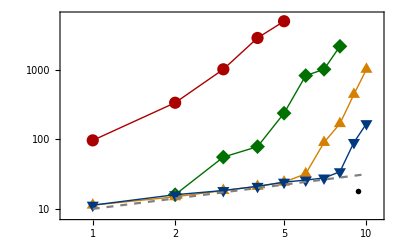

```mathematica
degree = 2;
straddles = {.2, 1,4,10};
markers = Graphics`PlotMarkers[][[{6,8,9,10}]];
markers = Graphics`PlotMarkers[][[{1,3,4,5}]];
markers[[All,2]] = 1.4*markers[[All,2]];

(* Importing *)
resultfiles = Table[
  FileNameJoin[ {NotebookDirectory[] ,"data3", 
"CTAPtree_d" <> ToString[degree] <> "_s" <> ToString[straddle] <> ".dat"
}]
,{straddle, straddles}];
ress = ReadList /@ resultfiles ;
nlevelss = Table[ DeleteDuplicates@res[[All,1]], {res, ress} ];
Ts = Table[ DeleteDuplicates@res[[All,2]], {res, ress}];

(* Plotting *)
tartimess2 =  Table[ findTargetTimesFlat[res, .05 ], {res,ress}];
tstarplt2 = Table[ 
ListLogLogPlot[ tartimess2[[j]]
, PlotStyle->elementarycols[[j]]
, FrameLabel->{MaTeX["k", Magnification->2], MaTeX["T^*/J", Magnification->2]}
, FrameTicks -> {{Automatic, Automatic}, {Join[Range[1,4],{6,9,12}] ,  Automatic}}
, PlotLabel->MaTeX["\\text{Constant error times versus tree depth}", Magnification->1.2]
 ,PlotRange-> {{.8,11},{8,6000}}
, PlotMarkers->markers[[j]]
 ]
,{j,1,Length[tartimess2]}];

baseplot = LogLogPlot[ 10 x^(1/2), {x,Min[nlevelss], Max[nlevelss]}, PlotStyle->{Gray, Dashed}];

leg =LineLegend[ elementarycols , straddles , LegendLabel->MaTeX["\\text{Straddling}", Magnification-> 1.2], LegendMarkers -> markers ] ;

treeTstars2 = Legended[
Show[{tstarplt2,baseplot},Epilog-> Inset[MaTeX["k^{0.5}", Magnification->1.7], Log[{9.3,18}] ]
(* , GridLines-> {{},Log[Ts[[1]]] }  *)
], leg ]
```

```mathematica
Export["treeTstars.pdf", treeTstars2]
```

treeTstars.pdf

#### Import and target times (d=3)

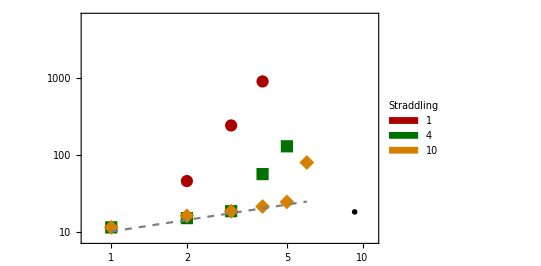

```mathematica
degree = 3;
straddles = { 1,4,10};
markers = Graphics`PlotMarkers[];
markers[[All,2]] = 1.4*markers[[All,2]];

(* Importing *)
resultfiles = Table[
  FileNameJoin[ {NotebookDirectory[] ,"data3", 
"CTAPtree_d" <> ToString[degree] <> "_s" <> ToString[straddle] <> ".dat"
}]
,{straddle, straddles}];
ress = ReadList /@ resultfiles ;
nlevelss = Table[ DeleteDuplicates@res[[All,1]], {res, ress} ];
Ts = Table[ DeleteDuplicates@res[[All,2]], {res, ress}];

(* Plotting *)
tartimess3 =  Table[ findTargetTimesFlat[res, .05 ], {res,ress}];
tstarplt = Table[ 
ListLogLogPlot[ tartimess3[[j]]
, PlotStyle->elementarycols[[j]]
, FrameLabel->{MaTeX["k", Magnification->2], MaTeX["T^*/J", Magnification->2]}
, FrameTicks -> {{Automatic, Automatic}, {Join[Range[1,4],{6,9,12}] ,  Automatic}}
, PlotLabel->MaTeX["\\text{Constant error times versus tree depth}", Magnification->1.2]
 ,PlotRange-> {{.8,11},{8,6000}}
, PlotMarkers->markers[[j]]
 ]
,{j,1,Length[tartimess3]}];

baseplot = LogLogPlot[ 10 x^(1/2), {x,Min[nlevelss], Max[nlevelss]}, PlotStyle->{Gray, Dashed}];

leg = SwatchLegend[ elementarycols , straddles , LegendLabel->"Straddling" ] ;

treeTstars3 = Legended[
Show[{tstarplt,baseplot},Epilog-> Inset[MaTeX["k^{0.5}", Magnification->1.7], Log[{9.3,18}] ]
(* , GridLines-> {{},Log[Ts[[1]]] }  *)
], leg ]
```

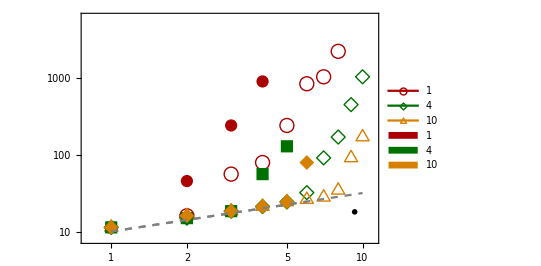

```mathematica
Show[ { treeTstars2, treeTstars3} ]
```

#### Import and target times (d=1, line)

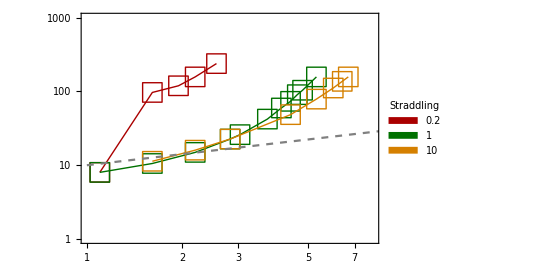

```mathematica
degree = 1;
straddles = {.2, 1,10};

(* Importing *)
resultfiles = Table[
  FileNameJoin[ {NotebookDirectory[] ,"data3", 
"CTAPtree_d" <> ToString[degree] <> "_s" <> ToString[straddle] <> ".dat"
}]
,{straddle, straddles}];
ress = ReadList /@ resultfiles ;
nlevelss = Table[ DeleteDuplicates@res[[All,1]], {res, ress} ];
Ts = Table[ DeleteDuplicates@res[[All,2]], {res, ress}];

(* Plotting *)
tartimess1 =  Table[ findTargetTimesFlat[res, .05 ], {res,ress}];

TvsV1 = Table[ tartimesPerLogV[tartimes, degree] , {tartimes,tartimess1} ];


tstarplt = Table[ 
ListLogLogPlot[ TvsV1[[j]]
, PlotStyle->elementarycols[[j]]
, FrameLabel->{MaTeX["Log[|V|]", Magnification->2], MaTeX["T^*/J", Magnification->2]}
, FrameTicks -> {{Automatic, Automatic}, {Join[Range[1,4],{6,9,12}] ,  Automatic}}
, PlotLabel->MaTeX["\\text{Constant error times versus tree depth}", Magnification->1.2]
, PlotMarkers->{"□",20}
, PlotRange->{{1,8},{1,1000} }
 ]
,{j,1,Length[tartimess1]}];

baseplot = LogLogPlot[ 10 x^(1/2), {x,Min[nlevelss], Max[nlevelss]}, PlotStyle->{Gray, Dashed}];

leg = SwatchLegend[ elementarycols , straddles , LegendLabel->"Straddling" ] ;

treeTstars1 = Legended[
Show[{tstarplt,baseplot},Epilog-> Inset[MaTeX["k^{0.5}", Magnification->1.7], Log[{9.3,18}] ]
(* , GridLines-> {{},Log[Ts[[1]]] }  *)
], leg ]
```

```mathematica
tartimess1
```

{{{1,8.},{2,97.0059},{4,∞},{8,∞},{16,∞},{32,∞},{64,∞},{128,∞},{256,∞}},{{1,8.},{2,10.5561},{4,14.9285},{8,22.6274},{10,25.9921},{20,42.2243},{30,59.7141},{40,73.5167},{50,90.5097},{60,103.968},{100,157.586},{400,∞}},{{2,11.3137},{4,16.},{8,22.6274},{40,48.5029},{100,78.7932},{200,111.43},{300,137.187},{400,157.586}}}

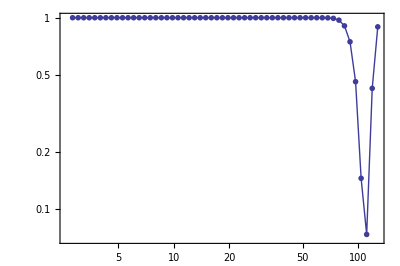

```mathematica
ListLogLogPlot[ Select[ress[[1]], #[[1]] == 16 & ][[All,{2,3}]] ]
```

#### Together: Tartimes versus LogV and versus k

```mathematica
TreeSimulationTargetTimes[ straddle_, degree_, errorgoal_:0.05 ]:= Module[{resultfile, res},
	resultfile = FileNameJoin[ {NotebookDirectory[] ,"data3", "CTAPtree_d" <> ToString[degree] <> "_s" <> ToString[straddle] <> ".dat"} ];
	res = ReadList@resultfile ;
	Return[ findTargetTimesFlat[res, errorgoal ] ];
];

TreeSimulationRes[ straddle_, degree_, errorgoal_:0.05 ]:= Module[{resultfile, res},
	resultfile = FileNameJoin[ {NotebookDirectory[] ,"data3", "CTAPtree_d" <> ToString[degree] <> "_s" <> ToString[straddle] <> ".dat"} ];
	Return[ ReadList@resultfile ];
];
```

```mathematica
{ Range[10], nlevelsToV[ Range[10], 3 ] } // MatrixForm
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
15 | 51 | 159 | 483 | 1455 | 4371 | 13119 | 39363 | 118095 | 354291)

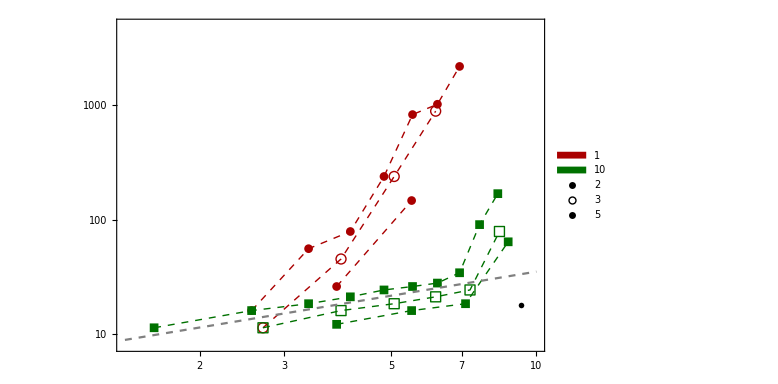

```mathematica
straddles = {1,10};
degrees = {2,3,5};
markers = { Graphics`PlotMarkers[], Graphics`PlotMarkers[][[6;;]], Graphics`PlotMarkers[] };
cols = elementarycols;
pltrange  = {{1.4,10},{8,5000}} ;

tartimesss = Table[ tartimesPerLogV[ TreeSimulationTargetTimes[ s, d ] , d ], {s,straddles}, {d,degrees} ];

plts = Table[ 
ListLogLogPlot[ tartimesss[[sidx,didx]]
, Joined -> True
, PlotStyle-> {elementarycols[[sidx]], Dashed }
, FrameLabel->{MaTeX["\\log( |V| )", Magnification->2], MaTeX["T^*/J", Magnification->2]}
, FrameTicks -> {{Automatic, Automatic}, {Automatic, Automatic}}
, PlotLabel->MaTeX["\\text{Constant error times versus tree depth}", Magnification->1.2]
, PlotMarkers->markers[[didx,sidx]]
, PlotRange->pltrange
]
 , { sidx, 1, Length[straddles]}, {didx, 1, Length[degrees]}   ];

baseplot = LogLogPlot[ 7 x^.7, {x,pltrange[[1,1]],pltrange[[1,2]]}, PlotStyle->{Gray, Dashed}];

leg = SwatchLegend[ elementarycols , straddles , LegendLabel->"Straddling" ] ;
dleg = SwatchLegend[ ConstantArray[ Black, Length[degrees] ], degrees, LegendMarkers-> { markers[[1,1]], markers[[2,1]] }
, LegendLabel-> "Degree" ];

treeTvsVplts = Legended[
Show[ {plts, baseplot}
 ,Epilog-> Inset[MaTeX["k^\\beta", Magnification->1.7], Log[{9.3,18}] ]
(* , GridLines-> {{},Log[Ts[[1]]] }  *)
, ImageSize-> Large
], {leg,dleg} ]
```

#### Together (old)

```mathematica
TreeSimulationTargetTimes[ straddle_, degree_, errorgoal_:0.05 ]:= Module[{resultfile, res},
	resultfile = FileNameJoin[ {NotebookDirectory[] ,"data3", "CTAPtree_d" <> ToString[degree] <> "_s" <> ToString[straddle] <> ".dat"} ];
	res = ReadList@resultfile ;
	Return[ findTargetTimesFlat[res, errorgoal ] ];
];

TreeSimulationRes[ straddle_, degree_, errorgoal_:0.05 ]:= Module[{resultfile, res},
	resultfile = FileNameJoin[ {NotebookDirectory[] ,"data3", "CTAPtree_d" <> ToString[degree] <> "_s" <> ToString[straddle] <> ".dat"} ];
	Return[ ReadList@resultfile ];
];
```

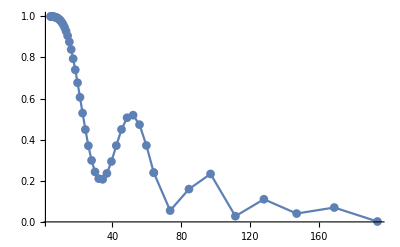

```mathematica
res4 = TreeSimulationRes[ 10, 4 ] ;
ListPlot[  Select[ res4, #[[1]] == 5  & ][[All,{2,3}]] ]
```

```mathematica
degree = 4;
straddles = {1,10};

(* Plotting *)
tartimess4 =  Table[TreeSimulationTargetTimes[ s, degree ], {s,straddles}];
TvsV4 = Table[ tartimesPerLogV[tartimes, degree] , {tartimes,tartimess4} ];
```

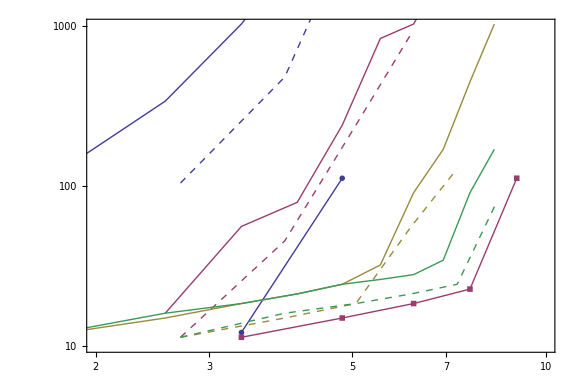

```mathematica
TvsV1 = Table[ tartimesPerLogV[tartimes, 1] , {tartimes,tartimess1} ];
TvsV2 = Table[ tartimesPerLogV[tartimes, 2] , {tartimes,tartimess2} ];
TvsV3 = Table[ tartimesPerLogV[tartimes, 3] , {tartimes,tartimess3} ];
Show[ {
ListLogLogPlot[ TvsV4 ]
, ListLogLogPlot[ TvsV3,PlotMarkers->None, Joined-> True, PlotStyle->Dashed ] 
,ListLogLogPlot[ TvsV2, PlotMarkers->None]

(*,  ListLogLogPlot[ TvsV1 ]  *)

}
, PlotRange-> Log[ { {2,10},{10,1000} } ] ]
```

```mathematica
Log[ nlevelsToV[ 4, 4] ] // N
```

7.62315

## Pretty tree graph

```mathematica
(* Tree construction methods *)

(* Given the root, this function returns (degree) leafs attached to the root *)
growLeafsFromRoot[ root_, degree_ ] := Module[{newvtx, newedges},
	newvtx = Table[ Append[ root, j ] , {j,0, degree-1} ];
	newedges = Table[ root <-> v, {v,newvtx} ];
	Return[{newvtx, newedges} ];
];

(* Given a set of roots, this function returns (degree) leafs grown from each of the roots *)
growLayerFromRoots[ roots_, degree_ ]:= Module[{newlayer, newvtxs, newedges},
	newlayer = Table[ growLeafsFromRoot[ root, degree ], {root, roots} ];
	(* newlayer has shape (nroots, 2), where the 2 represents (newvtx, newedges) *)
	newvtxs = Flatten[ newlayer[[All,1]], 1 ];
	newedges = Flatten[ newlayer[[All,2]], 1 ];
	Return[{newvtxs, newedges}];
];

(* Given a set of degrees, build the corresponding tree *)
growTree[ degrees_, root_:{} ] := Module[{nlayers, vtxlist, edgelist, newvtxs, newedges},

	nlayers = Length[degrees]+1;
	vtxlist ={  {root}   };
	edgelist = {};
	
	Do[
		{newvtxs, newedges} = growLayerFromRoots[ vtxlist[[-1]] , degrees[[l]]  ];
		AppendTo[ vtxlist, newvtxs ];
		AppendTo[ edgelist, newedges ];
		, {l, 1, nlayers-1}];
	Return[{vtxlist, edgelist} ];
];

(* Grow the subdivided tree specific for CTAP *)
SubdividedTreeGraph[ degrees_ ]:= Module[{subddegrees, vtxlist, edgelist },
	subddegrees = {degrees, ConstantArray[1, Length@degrees]}ᵀ // Flatten;
	{vtxlist, edgelist} = growTree[ subddegrees, {} ];
	Return[ Graph[ Flatten[vtxlist, 1] , Flatten[edgelist, 1 ] ] ];
];
```

```mathematica
g = Graph[ SubdividedTreeGraph[{2,2}], VertexStyle ->  Gray,VertexSize->Large, EdgeStyle->{Black, Thickness[.03]} ];
```

```mathematica
Export["g.pdf",g]
```

ItemAspectRatio::shdw: Symbol ItemAspectRatio appears in multiple contexts {System`,Global`}; definitions in context System` may shadow or be shadowed by other definitions.

g.pdf